```mathematica
P[z_] = GeneratingFunction[PDF[PoissonDistribution[λ], n], n, z]
```

ⅇ^((-1+z) λ)

```mathematica
Series[P[z], {z, 0, 5}]
```

ⅇ^-λ+ⅇ^-λ λ z+1/2 ⅇ^-λ λ^2 z^2+1/6 ⅇ^-λ λ^3 z^3+1/24 ⅇ^-λ λ^4 z^4+1/120 ⅇ^-λ λ^5 z^5+O[z]^6

```mathematica
CoefficientList[ⅇ^-λ+ⅇ^-λ λ z+1/2 ⅇ^-λ λ^2 z^2+1/6 ⅇ^-λ λ^3 z^3+1/24 ⅇ^-λ λ^4 z^4+1/120 ⅇ^-λ λ^5 z^5+O[z]^6,z]
```

{ⅇ^-λ,ⅇ^-λ λ,1/2 ⅇ^-λ λ^2,1/6 ⅇ^-λ λ^3,1/24 ⅇ^-λ λ^4,1/120 ⅇ^-λ λ^5}

```mathematica
SeriesCoefficient[P[z], {z, 0, 3}] /.{λ -> 2}
```

4/(3 ⅇ^2)

```mathematica
SeriesCoefficient[P[z], {z, 0, 3}] /.{λ -> 2} // N
```

0.180447

```mathematica
SeriesCoefficient[P[z], {z, 0, 3}] /.{λ -> 2.}
```

0.180447

```mathematica
D[P[z], z] /. z-> 1
```

λ

```mathematica
D[P[z], {z, 3}]
```

ⅇ^((-1+z) λ) λ^3

```mathematica
(* transformata Laplace'a Stieltjesa *)
F[s_]=LaplaceTransform[PDF[ExponentialDistribution[µ], t],t,s]
```

µ/(s+µ)

```mathematica
(* dla sumy zmiennych losowych / jest to iloczyn *)
(* informacje o wartości oczekiwanej *)
-D[F[s], s]/.s->0
```

1/µ

```mathematica
(* gęstość rozkładu *)
g[t_]=InverseLaplaceTransform[F[s],s,t]
```

ⅇ^(-t µ) µ

```mathematica
(* dystrybuanta, całka z tego wyżej *)
Integrate[g[t],{t,0,x}]
```

1-ⅇ^(-x µ)

### Proces Poissona

```mathematica
M = PoissonProcess[λ]
```

PoissonProcess[λ]

```mathematica
PoissonProcess[µ][t]
```

PoissonDistribution[t µ]

```mathematica
Probability[m[t] < 4, m\[Distributed]M]
```

1/6 ⅇ^(-t λ) (6+6 t λ+3 t^2 λ^2+t^3 λ^3)

```mathematica
Probability[m[t] == k, m\[Distributed]M]
```

Piecewise[{{(ⅇ^(-t λ) (t λ)^k)/(k!), k==Floor[k]&&k≥0}, {0, True}}]

```mathematica
Assuming[k∈Integers && k ≥ 0, Probability[m[t] == k, m\[Distributed]M]]
```

(ⅇ^(-t λ) (t λ)^k)/(k!)

```mathematica
p[k_,t_]=PDF[M[t],k]
```

Piecewise[{{(ⅇ^(-t λ) (t λ)^k)/(k!), k≥0}, {0, True}}]

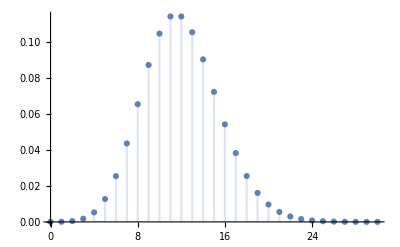

```mathematica
DiscretePlot[p[k, 4]/.λ->3, {k,0,30}]
```

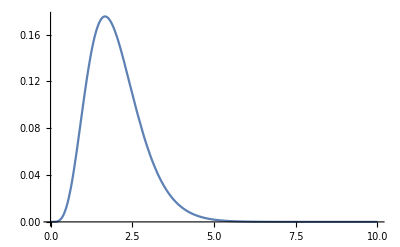

```mathematica
Plot[p[5,t]/.λ ->3, {t,0,10}]
```

```mathematica
(* generowanie procesu Poissona -> funkcja, nie zmienna *)
RandomVariate[ExponentialDistribution[2]]
```

0.86192

```mathematica
RandomVariate[PoissonDistribution[2]]
```

1

```mathematica
proces = RandomFunction[M/.λ->7, {0, 5}]
```

TemporalData[…]

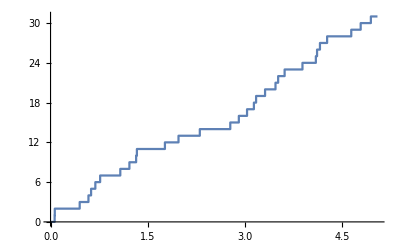

```mathematica
ListStepPlot[proces]
```

```mathematica
(* to się niby może przydać w zad.3*)
Probability[X==Min[X,Y], {X\[Distributed]ExponentialDistribution[λ], Y\[Distributed]ExponentialDistribution[µ]}]
```

λ/(λ+µ)

```mathematica
Probability[m[1.5]==0,m\[Distributed]M] (* a) tyle wynosi proawdopodobienstwo *)
```

ⅇ^(-1.5 λ)

```mathematica
(* b *)
Probability[m[1.5]==2,m\[Distributed]M]
```

1.125 ⅇ^(-1.5 λ) λ^2

```mathematica
(* c - wartość kary *)
kara[λ_]=Expectation[50m[1.5],m\[Distributed]M]
```

75. λ

```mathematica
(* c - ryzyko opłacalności *)
```

```mathematica
Reduce[{kara[λ]<5*1.5, λ>0},λ]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

0<λ<0.1

```mathematica
(* jeżeli lambda przekroczy 0.1 ryzyko będzie nieopłacalne *)
```